```mathematica
This file estimates the concentration of MT formation (and other intermediates) based on the ODE model
```

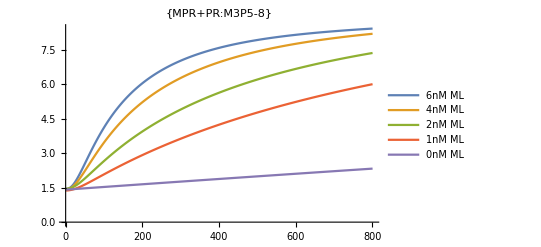

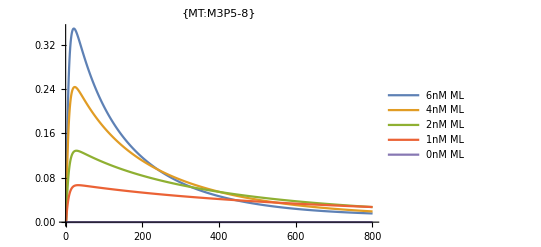

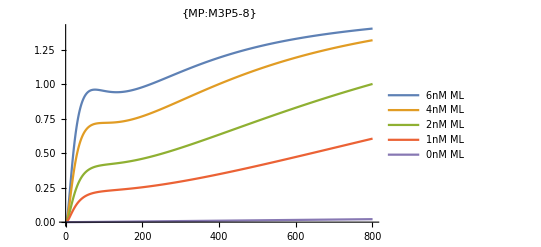

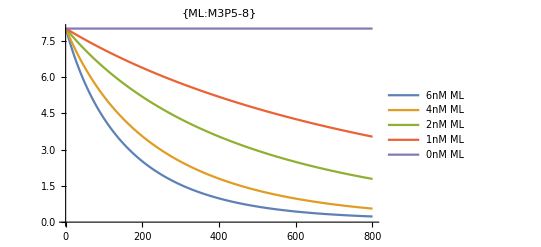

```mathematica
Btype={"B1","B1a","B1b"};
Ptype={"P29-5","P28-5","P27-5"};
Mtype={"M1","M2","M3"};
MPtype={"P5-6","P5-7","P5-8"};
For[Ii=3,Ii<=3,Ii++,
For[J=3,J<=3,J++,

type=Btype[[Ii]];
ty=Mtype[[Ii]];
proof=Ptype[[J]];
mproof=MPtype[[J]];
tend=800;
Clear[a,b,c,x,y,z,k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,t,C1,C2,C3,C4,C5,C6,C3a,C1a];
SetDirectory[ParentDirectory[NotebookDirectory[]]];
(*Import all rates*)
k1=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[1]];
k2=Import["1. Lock opening and binding\\Rates\\"<>type<>"klock.wl"][[2]];
k3=Import["BT+P rates\\"<>type<>proof<>".wl"][[1]];
k4=Import["BT+P rates\\"<>type<>proof<>".wl"][[2]];
k5=Import["BP+RQ rates\\"<>type<>proof<>".wl"][[1]];
k6=Import["BP+RQ rates\\"<>type<>proof<>".wl"][[2]];
k7=Import["BT+P rates\\"<>type<>proof<>".wl"][[3]];
data=Import["4. Discard Pathway\\Sim\\"<>type<>proof<>".wl"];
data2=Import["4. Discard Pathway\\Data\\"<>type<>proof<>".wl"];
k7=k7;
k8=0;
k9=0;
k10=0;
k11=0;
(*C1: concentration with domain B/M: ML, MT, MP, MPR, MN (dimer), MNR(dimer with reporter: [ML]o*)
(*C2: Concentration with domain P: P, MP, MPR, PR:[Po]*)
(*C3: Concentration with domain T: MT, T:{1,2,4,6}*)
(*C4: Concentration with domain R: MNR, RQ, MPR, PR: [RQ]o*)
(*C5: Concentration with domain Q: RQ, Q: [RQ]o*)
(*C6: Concentration with domain L: ML, L: [ML]o*)
(*C7: Concentration with domain N: N, MN, MNR: [N]o*)
(*x:[MT], y: [MP]; z: [MPR], a: [PR], b: [MN], c: [MNR]*)
(* [ML]=C1-x-y-z-b-c;
[T]=C3-x;
[L]=C6-[ML]=C6-C1+x+y+z+b+c;
[P]=C2-y-z-a;
[RQ]=C4-a-c-z;
[Q]=C5-[RQ]=C5-C4+a+c+z
[N]=C7-b-c
*)
concBPRi=data[[1;;,1]][[1;;,2]];

concT={6,4,2,1,0};
RQo=20;
data3={Table[t,{t,0,tend}]};(*Stores [MPR]+[PR]*)
data4={Table[t,{t,0,tend}]};(*Stored [MT]*)
data5=data4;
data6=data4;
For[i=1,i<=Length[concT],i++,
C1=8+concBPRi[[i]];
C6=8;
C2=50+concBPRi[[i]];
C3=concT[[i]];
C4=RQo+concBPRi[[i]];
C5=RQo;
C7=0;
(*ODE model*)
sol=NDSolve[{x'[t]==k1*(C1-x[t]-y[t]-z[t]-b[t]-c[t])*(C3-x[t])-k2*x[t]*(C6-C1+x[t]+y[t]+z[t]+b[t]+c[t])-k3*x[t]*(C2-a[t]-y[t]-z[t])+k4*y[t]*(C3-x[t])-k8*x[t]*(C7-b[t]-c[t])+k9*b[t]*(C3-x[t]),

y'[t]==k3*x[t]*(C2-a[t]-y[t]-z[t])-k4*y[t]*(C3-x[t])-k5*y[t]*(C4-z[t]-a[t]-c[t])+k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

z'[t]==k5*y[t]*(C4-z[t]-a[t]-c[t])-k6*z[t]*(C5-C4+z[t]+a[t]+c[t]),

a'[t]==k7*(C2-y[t]-z[t]-a[t])*(C4-a[t]-c[t]-z[t]),

b'[t]==k8*x[t]*(C7-b[t]-c[t])-k9*b[t]*(C3-x[t])-k10*b[t]*(C4-a[t]-c[t]-z[t])+k11*c[t]*(C5-C4+z[t]+a[t]+c[t]),

c'[t]==k10*b[t]*(C4-a[t]-c[t]-z[t])-k11*c[t]*(C5-C4+z[t]+a[t]+c[t])
,
x[0]==0,y[0]==0,z[0]==concBPRi[[i]],a[0]==0,b[0]==0,c[0]==0},{x,y,z,a,b,c},{t,0,tend}];

AppendTo[data3,Table[(a[t]+z[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data4,Table[(x[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data5,Table[(y[t])/.sol[[1]],{t,0,tend}]];
AppendTo[data6,Table[(C1-x[t]-y[t]-z[t]-b[t]-c[t])/.sol[[1]],{t,0,tend}]];

];

s3=ListPlot[data3[[2;;6]],Joined->True,PlotLabel->{"MPR+PR:"<>ty<>mproof},PlotLegends->{"6nM ML","4nM ML","2nM ML","1nM ML","0nM ML"}];
s4=ListPlot[data4[[2;;6]],Joined->True,PlotRange->All,PlotLabel->{"MT:"<>ty<>mproof},PlotLegends->{"6nM ML","4nM ML","2nM ML","1nM ML","0nM ML"}];
s5=ListPlot[data5[[2;;6]],Joined->True,PlotRange->All,PlotLabel->{"MP:"<>ty<>mproof},PlotLegends->{"6nM ML","4nM ML","2nM ML","1nM ML","0nM ML"}];
s6=ListPlot[data6[[2;;6]],Joined->True,PlotRange->All,PlotLabel->{"ML:"<>ty<>mproof},PlotLegends->{"6nM ML","4nM ML","2nM ML","1nM ML","0nM ML"}];

Print[s3];
Print[s4];
Print[s5];
Print[s6];
(*
SetDirectory["4. Discard pathway\\MT prediction"];
Export[type<>proof<>".xlsx",Transpose[data4]]*)
]]
```